276114

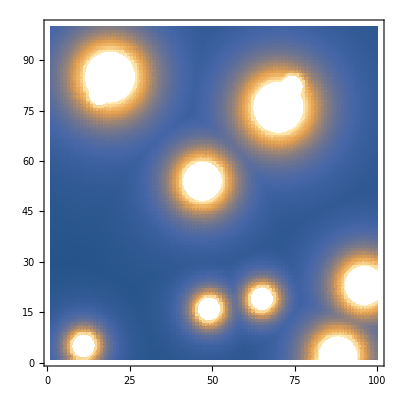

(19 | 65 | 100
5 | 11 | 100
16 | 49 | 100
80 | 16 | 100
82 | 74 | 100
23 | 96 | 300
2 | 88 | 300
54 | 47 | 300
85 | 19 | 500
76 | 70 | 500)

-Graphics3D-

```mathematica
mapp = Table[0, {i,100}, {j,100}];
tower= Table[0,{i,10},{j,3}];
human= Table[RandomInteger[{1,100}],{i,100}, {j,100}];
ListPlot3D[human];
SetMapp=Module[{},
For[i=1, i≤10,i++,
	x=RandomInteger[{1,100}];
	y=RandomInteger[{1,100}];
	While [mapp[[x,y]]≠ 0 , 
		x=RandomInteger[{1,100}];
		y=RandomInteger[{1,100}];
	];
	tower[[i,1]]=x;
	tower[[i,2]]=y;
	Which [i≤5,mapp[[x,y]]=100; tower[[i,3]]=100, 
		 i≥6 && i≤8, mapp[[x,y]]=300; tower[[i,3]]=300,
	          i≥9 , mapp[[x,y]]=500; tower[[i,3]]=500
          ];
];
];
(*ListPlot3D[];*)
MatrixForm[tower];
For[ i=1, i ≤100, i++,
For [j =1 , j≤100, j++,
For [k=1, k≤10, k++,
x = tower[[k,1]];
y=tower[[k,2]];
If[x==i && y==j,
mapp[[i,j]]=tower[[k,3]];
Continue[]];
d =  (i - x)^2 + (j - y)^2 ;

mapp[[i,j]]= Max[mapp[[i,j]],tower[[k,3]] / d];
]]];
count= 0;
For[ i=1, i ≤100, i++,
For [j =1 , j≤100, j++,
If[mapp[[i,j]]>1, count+= human[[i,j]]]
]];
Print[count];
ListDensityPlot[mapp]
MatrixForm[tower]
ListPlot3D[human]
```